# Separable ordinary differential equations

## Simple example problem

The variable of the differential equation dy/dx=x can be separated

Such a separation yields dy=xdx

Integrating both sides yields ∫ⅆy=∫xⅆx

The solution is thus y(x)=1/2 x^2+c

```mathematica
DSolve[{y'[x]==x},y[x],x]
```

{{y[x]→x^2/2+C[1]}}

## Adding an initial value

Solve dy/dx=x^2-1,y(0)=4 (initial value problem, IVP)

```mathematica
DSolve[{y'[x]==x^2-1,y[0]==2},y[x],x]
```

{{y[x]→1/3 (6-3 x+x^3)}}

This solution can be simplified using the Expand[] function

```mathematica
Expand[DSolve[{y'[x]==x^2-1,y[0]==2},y[x],x]]
```

{{y[x]→2-x+x^3/3}}

We can use //TraditionalForm to print a better looking solution

```mathematica
Expand[DSolve[{y'[x]==x^2-1,y[0]==2},y[x],x]]//TraditionalForm
```

{{y(x)→x^3/3-x+2}}

## Plotting the slope field and the IVP solution

We can plot the slope field

The derivative at every point is the slope at every point

First we’ll plot the slope field of dy/dx=x^2-1

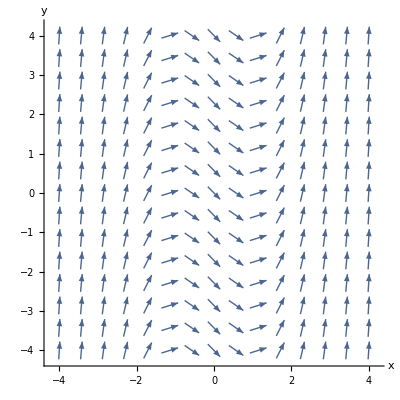

```mathematica
VectorPlot[{1,x^2-1},{x,-4,4},{y,-4,4},VectorScale->{0.04,0.04,None},Frame->None,Axes->True,AxesLabel->{"x","y"}]
```

Now we will add the solution graph

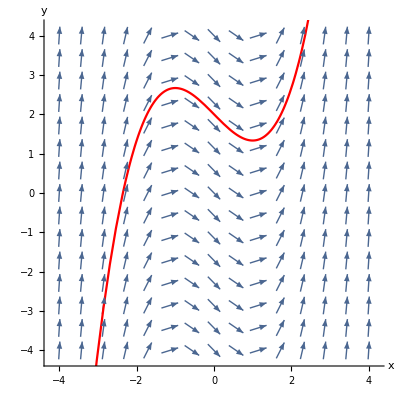

```mathematica
Show[VectorPlot[{1,x^2-1},{x,-4,4},{y,-4,4},VectorScale->{0.04,0.04,None}],Plot[x^3/3-x+2,{x,-4,4},PlotStyle->Red],Frame->None,Axes->True,AxesLabel->{"x","y"}]
```

## Clearing variables in case of assignments

In case you ever assigned a value by mistake, i.e. y'[x]=3xinstead of y'[x]==3x, clear it before calculating another ODE (whichever of the examples below is / are appropriate):

```mathematica
(*
y'[x]=.;
y[x]=.;
y[0]=.;
*)
```

## Another example

Solve dy/dx=3y,y(0)=-2

```mathematica
DSolve[y'[x]==3y[x],y[x],x]
```

{{y[x]→ⅇ^(3 x) C[1]}}

```mathematica
DSolve[{y'[x]==3y[x],y[0]==-2},y[x],x]
```

{{y[x]→-2 ⅇ^(3 x)}}

Let’s plot it

Notice that dy/dx=3y is an autonomous function, i.e. the derivative is not dependent upon the independent variable

The slope field will show this as a similar slope for all values of x for every value of y

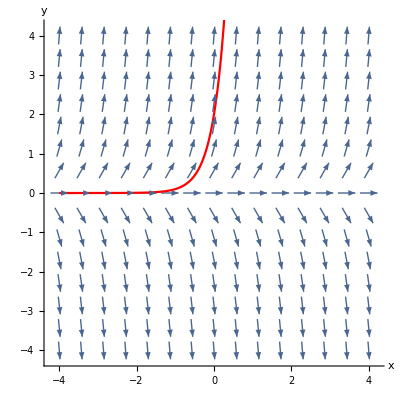

```mathematica
Show[VectorPlot[{1,3y},{x,-4,4},{y,-4,4},VectorScale->{0.04,0.04,None}],Plot[2 ⅇ^(3x),{x,-4,4},PlotStyle->Red],Frame->None,Axes->True,AxesLabel->{"x","y"}]
```

## Plotting more than one solution by specifying the arbitrary constant

Solve dy/dx=-y

In order to re-use the solution, we will assign it to the computer variable sol

```mathematica
sol=DSolve[y'[x]==-y[x],y[x],x]
```

{{y[x]→ⅇ^-x C[1]}}

Let’s calculate the solution setting C[1]→2, i.e. c_1=2

```mathematica
y[x]/.sol/.C[1]->2
```

{2 ⅇ^-x}

Plot for c=2 and c=3

```mathematica
y[x]/.sol/.C[1]->2
```

{2 ⅇ^-x}

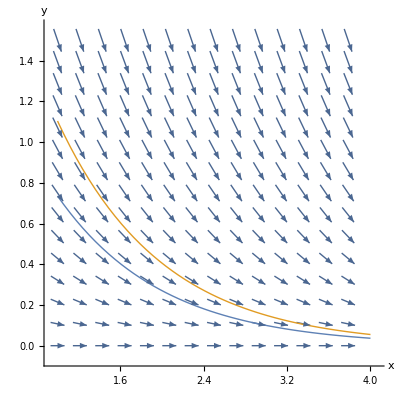

```mathematica
Show[VectorPlot[{1,-y},{x,1,4},{y,0,1.5},VectorScale->{0.04,0.04,None}],Plot[{y[x]/.sol/.C[1]->2,y[x]/.sol/.C[1]-> 3},{x,1,4},PlotStyle->Thick],Frame->None,Axes->True,AxesLabel->{"x","y"}]
```

## Examples

Solve the autonomous ODE dy/dx=y^2-4

```mathematica
DSolve[y'[x]==y[x]^2-4,y[x],x]
```

{{y[x]→-(2 (-1+ⅇ^(4 x+4 C[1])))/(1+ⅇ^(4 x+4 C[1]))}}

Solve dy/dx=ⅇ^(-x^2)

```mathematica
DSolve[y'[x]==ⅇ^(-x^2),y[x],x]//TraditionalForm
```

{{y(x)→c_1+1/2 √π erf(x)}}

Solve the autonomous ODE dy/dx=(y-1)^2

```mathematica
DSolve[y'[x]==(y[x]-1)^2,y[x],x]
```

{{y[x]→(-1+x+C[1])/(x+C[1])}}

Solve the above autonomous ODE with the initial value y(0)=0.01

```mathematica
DSolve[{y'[x]==(y[x]-1)^2,y[0]==0.01},y[x],x]
```

{{y[x]→(0.010101+x)/(1.0101+x)}}

Solve the autonomous ODE dy/dx=(y(3-y))/4

```mathematica
DSolve[y'[x]==1/4 (3-y[x]) y[x],y[x],x]
```

{{y[x]→(3 ⅇ^(3 x/4))/(ⅇ^(3 x/4)+ⅇ^(3 C[1]))}}

Note how the solution can never be negative.  This mean that we cannot have an initial value that is negative.  We can rewrite the solution:

```mathematica
y[x_]:=(3 ⅇ^(3 x/4))/(ⅇ^(3 x/4)+c)
```

Now we take the first derivative with respect to x

```mathematica
y'[x]
```

-(9 ⅇ^(3 x/2))/(4 (c+ⅇ^(3 x/4))^2)+(9 ⅇ^(3 x/4))/(4 (c+ⅇ^(3 x/4)))

Simplifying this

```mathematica
Simplify[-(9 ⅇ^(3 x/2))/(4 (c+ⅇ^(3 x/4))^2)+(9 ⅇ^(3 x/4))/(4 (c+ⅇ^(3 x/4)))]
```

(9 c ⅇ^(3 x/4))/(4 (c+ⅇ^(3 x/4))^2)

Now if we take the original ODE and then simplify it, we get the same solution

```mathematica
1/4*(y[x]*(3-y[x]))
```

(3 ⅇ^(3 x/4) (3-(3 ⅇ^(3 x/4))/(c+ⅇ^(3 x/4))))/(4 (c+ⅇ^(3 x/4)))

```mathematica
Simplify[1/4*(y[x]*(3-y[x]))]
```

(9 c ⅇ^(3 x/4))/(4 (c+ⅇ^(3 x/4))^2)

Solve the problem above with the initial value y(0)=2

```mathematica
Clear[y]
```

```mathematica
DSolve[{y'[x]==1/4 (3-y[x]) y[x],y[0]==2},y[x],x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y[x]→(6 ⅇ^(3 x/4))/(1+2 ⅇ^(3 x/4))}}

Plot the slope field and initial value curve

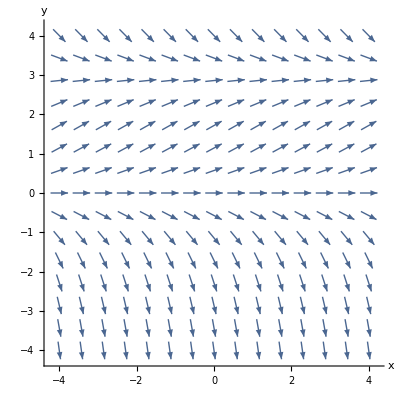

```mathematica
VectorPlot[{1,1/4 y (3-y)},{x,-4,4},{y,-4,4},VectorScale->{0.04,0.04,None},Frame->False,Axes->True,AxesLabel->{"x","y"}]
```

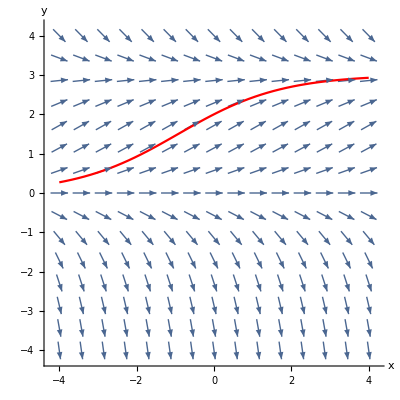

```mathematica
Show[VectorPlot[{1,1/4 y (3-y)},{x,-4,4},{y,-4,4},VectorScale->{0.04,0.04,None}],Plot[(6 ⅇ^(3 x/4))/(1+2 ⅇ^(3 x/4)),{x,-4,4},PlotStyle->Red],Frame->False,Axes->True,AxesLabel->{"x","y"}]
```

## Insights through visualizing the solution curve

We can gain insight into the solution curve by animation

Solve the IVP by setting the initial value to a variable k

```mathematica
DSolve[{y'[x]==1/4 (3-y[x]) y[x],y[0]==k},y[x],x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y[x]→(3 ⅇ^(3 x/4) k)/(3-k+ⅇ^(3 x/4) k)}}

Animating the solution over x and over the initial value variable k

```mathematica
Manipulate[Show[VectorPlot[{1,1/4 y (3-y)},{x,-8,8},{y,-4,4},VectorScale->{0.04,0.04,None}],Plot[(3 ⅇ^(3 x/4)*k)/(3-k+ⅇ^(3 x/4)*k),{x,-8,b},PlotStyle->Red],Frame->False,Axes->True,AxesLabel->{"x","y"}],{b,-7.99,8},{{k,2},-1,4}]
```

## Using pure functions

A function such as f:x↦x^2 in Mathematica can also be expressed as follows (called a pure function)

```mathematica
Function[{x},x^2]
```

Function[{x},x^2]

Values can be passed to calculate a solution

```mathematica
Function[{x},x^2][2]
```

4

We can store the output of DSolve[] as a pure function by solving for y instead of y[x] and using DSolveValue[]

```mathematica
solution=DSolveValue[{y'[x]==2x,y[0]==0},y,x]
```

Function[{x},x^2]

Solve and plot the ODE dy/dx=y^2,y(0)=y_0

```mathematica
Subscript[ϕ, y0_]=DSolveValue[{y'[x]==y[x]^2,y[0]==y0},y,x]
```

Function[{x},-y0/(-1+x y0)]

```mathematica
Manipulate[Show[VectorPlot[{1,y^2},{x,-4,4},{y,-4,4},VectorScale->{0.04,0.04,None}],Plot[Subscript[ϕ, y0][x],{x,-4,4},PlotStyle->Red,PlotRange->All],Axes->True,Frame->False],{{y0,2},-1,4}]
```

## YouTube example problems

```mathematica
Hyperlink["https://www.youtube.com/watch?v=oS07jI7uhzw&list=PLsu0TcgLDUiJF5u8tbcnyxjAFhqiSyGnJ&index=3"]
```

```mathematica
DSolve[y'[x]==y[x]/(1+x),y[x],x]//TraditionalForm
```

{{y(x)→c_1 (x+1)}}

```mathematica
Hyperlink["https://www.youtube.com/watch?v=oS07jI7uhzw&list=PLsu0TcgLDUiJF5u8tbcnyxjAFhqiSyGnJ&index=3"]
```

```mathematica
DSolve[{y'[x]==-x/y[x],y[4]==-3},y[x],x]
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{{y[x]→-√(25-x^2)}}

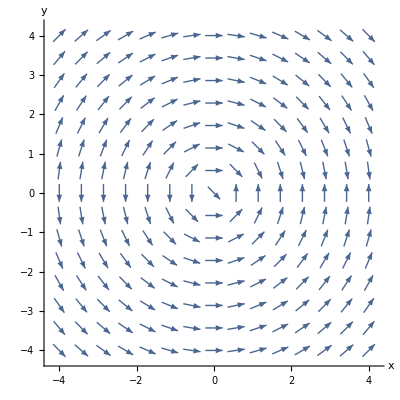

```mathematica
VectorPlot[{1,-x/y},{x,-4,4},{y,-4,4},VectorScale->{0.04,0.04,None},Frame->False,Axes->True,AxesLabel->{"x","y"}]
```

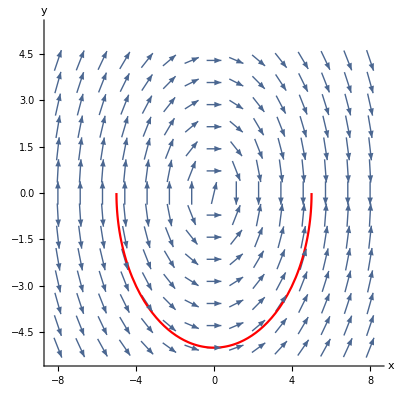

```mathematica
Show[VectorPlot[{1,-x/y},{x,-8,8},{y,-5,5},VectorScale->{0.04,0.04,None}],Plot[-√(25-x^2),{x,-5,5},PlotStyle->Red],Frame->False,Axes->True,AxesLabel->{"x","y"}]
```

```mathematica
Hyperlink["https://www.youtube.com/watch?v=MOw4qqduEvk&list=PLsu0TcgLDUiJF5u8tbcnyxjAFhqiSyGnJ&index=5"]
```

```mathematica
DSolve[y'[x]==y[x]^2-4,y[x],x]//Simplify
```

{{y[x]→(2-2 ⅇ^(4 (x+C[1])))/(1+ⅇ^(4 (x+C[1])))}}

```mathematica
Hyperlink["https://www.youtube.com/watch?v=1uiHZY9AgSo&index=6&list=PLsu0TcgLDUiJF5u8tbcnyxjAFhqiSyGnJ"]
```

```mathematica
DSolve[{y'[x]==(ⅇ^y[x]*Sin[2*x])/(Cos[x]*(ⅇ^(2*y[x])-y[x])),y[0]==0},y[x],x]
```

{{y[x]→InverseFunction[ⅇ^#1-ⅇ^-#1 (-1-#1)&][4-2 Cos[x]]}}

```mathematica
Hyperlinl["https://www.youtube.com/watch?v=Th7OHZQsKQQ&index=7&list=PLsu0TcgLDUiJF5u8tbcnyxjAFhqiSyGnJ"]
```

```mathematica
DSolve[{y'[x]==ⅇ^(-x^2),y[3]==5},y[x],x]//TraditionalForm
```

{{y(x)→1/2 (√π erf(x)-√π erf(3)+10)}}

```mathematica
Hyperlink["https://www.youtube.com/watch?v=jOHtED_ALME&index=8&list=PLsu0TcgLDUiJF5u8tbcnyxjAFhqiSyGnJ"]
```

```mathematica
DSolve[{y'[x]==(y[x]-y[x]*x)/x^2,y[1]==-1},y[x],x]
```

{{y[x]→-ⅇ^(1-1/x)/x}}

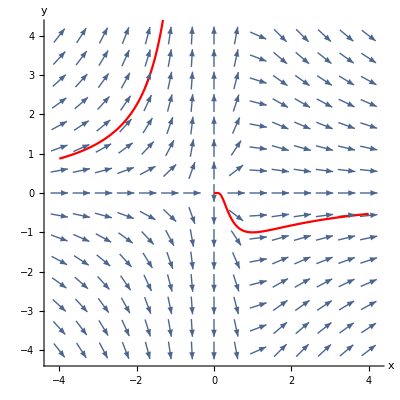

```mathematica
Show[VectorPlot[{1,(y-y*x)/x^2},{x,-4,4},{y,-4,4},VectorScale->{0.04,0.04,None}],Plot[-ⅇ^(1-1/x)/x,{x,-4,4},PlotStyle->Red],Frame->False,Axes->True,AxesLabel->{"x","y"}]
```